```mathematica
PlotCNN[b_,c_,k_,w_,h_,r_,s_,σ_]:=(
Print["ratio is ",(r*s/σ^2)^(1/2)];
LogLogPlot[{
b*c*(σ*h+s)*(σ*w+r),
b*k*h*w,
c*k*r*s,
b*c*k*w*h*r*s/m,
b*c*k*w*h*(r*s*σ^2/m)^(1/2),
b*c*k*w*h*r*s/m^(1/2)
}
,{m,1,10^8}
,PlotLegends->{"Img size", "Out size", "Filter size", "HBL large filter (BCKWHRS/M)", "HBL small filter BCKWH(RSσ_W/M)^(1/2)","Matmul Reuse"}
,AxesLabel->{"Cache Size (words)", "Comm. Cost (words)"}
,PlotStyle->{1,1,1,1,1,Dashed}
,GridLines->{{{121/16,Gray},{17424,Gray}},None}]
)
```

```mathematica
FindInt[b_,c_,k_,w_,h_,r_,s_,σ_]:=Solve[
(*b*c*k*w*h*r*s/m==b*c*k*w*h*(r*s*σ^2/m)^(1/2)*)
b*k*h*w==b*c*k*w*h*(r*s*σ^2/m)^(1/2)
,m]
```

Get tiling for this one!

```mathematica
Log[10.,Times[1000,1024,1024,96,111,111,11,11,4,4]]
```

18.3804

```mathematica
FindInt[1000,3,96,55,55,11,11,4]
```

{{m→17424}}

```mathematica
PlotCNN[1000,3,96,55,55,11,11,4]
```

ratio is 11/4

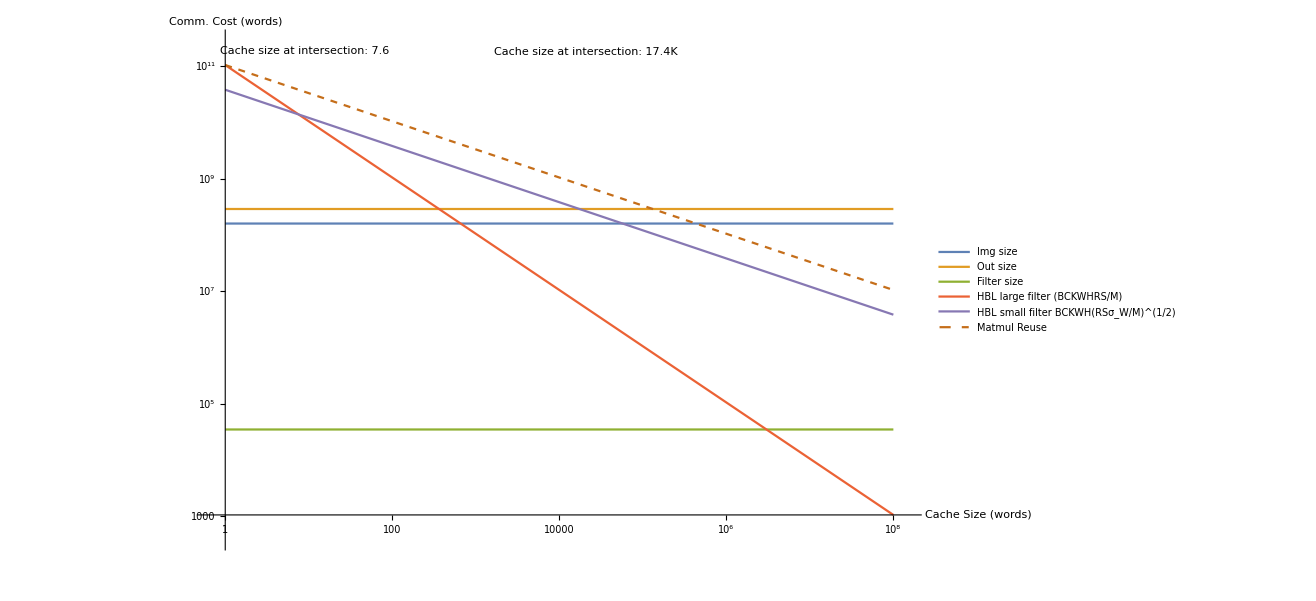

ratio is 11/4

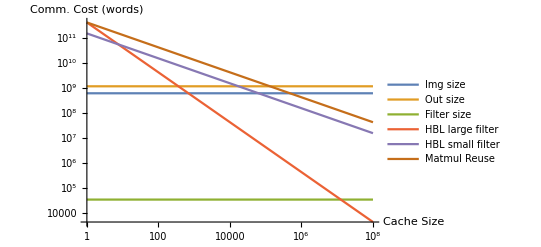

```mathematica
PlotCNN[1024,3,96,111,111,11,11,4]
```

ratio is 1

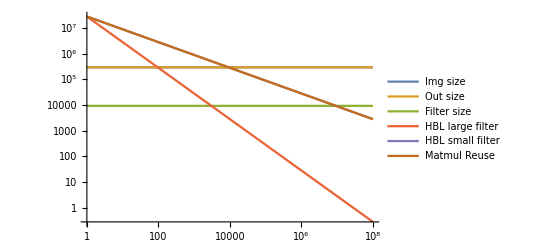

```mathematica
PlotCNN[96,96,55,55,1,1,1]
```

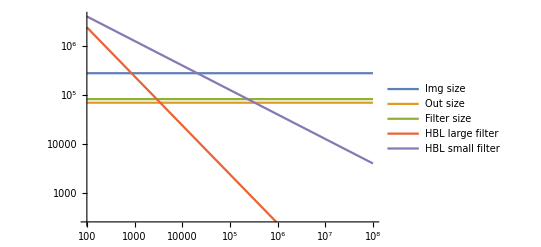

```mathematica
PlotCNN[96,96,27,27,3,3,2]
```

ratio is 5

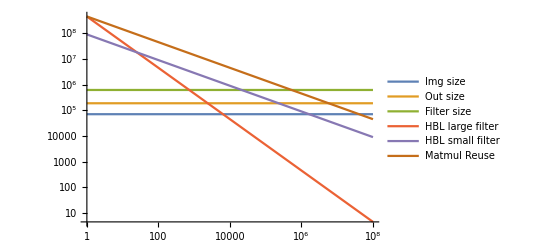

```mathematica
PlotCNN[96,256,27,27,5,5,1]
```

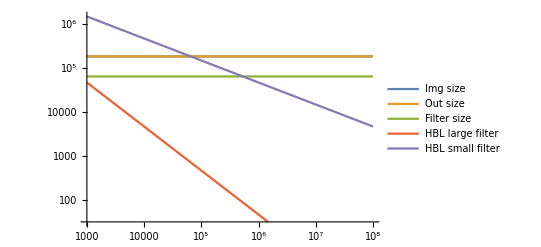

```mathematica
PlotCNN[256,256,27,27,1,1,1]
```

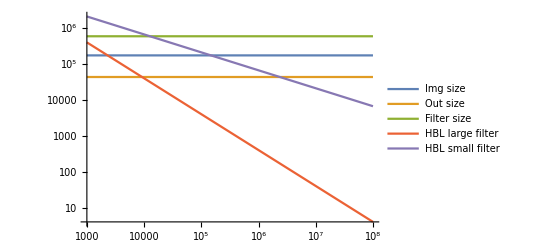

```mathematica
PlotCNN[256,256,13,13,3,3,2]
```

ratio is 3

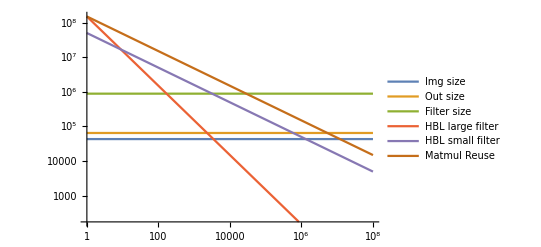

```mathematica
PlotCNN[256,384,13,13,3,3,1]
```

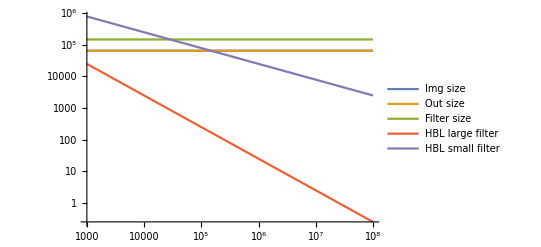

```mathematica
PlotCNN[384,384,13,13,1,1,1]
```

```mathematica
PlotCNN[384,384,13,13,1,1,1]
```

-Graphics-

ratio is 3

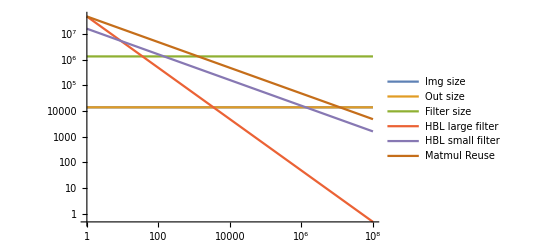

```mathematica
PlotCNN[384,384,6,6,3,3,1]
```

ratio is 3

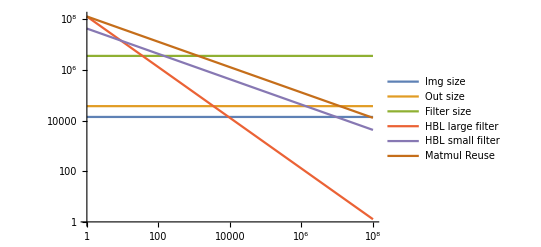

```mathematica
PlotCNN[384,1024,6,6,3,3,1]
```

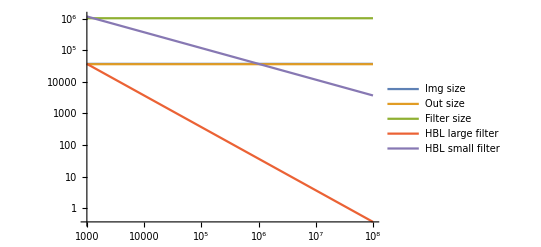

```mathematica
PlotCNN[1024,1000,6,6,1,1,1]
```

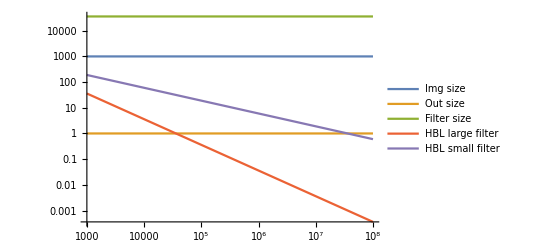

```mathematica
PlotCNN[1000,1,1,1,6,6,1]
```